## Finite Volume Methods

## Ch 13 Exercises

### (7)

#### (d)

```mathematica
u1[v_,Vstar_,Ustar_,p_]=Ustar+Sqrt[-(p[v]-p[Vstar])/(v-Vstar)](v-Vstar)
```

1+(-1+v) √((-2.27183+0.1 ⅇ^v+2 v)/(-1+v))

```mathematica
u2[v_,Vstar_,Ustar_,p_]=Ustar-Sqrt[-(p[v]-p[Vstar])/(v-Vstar)](v-Vstar)
```

1-(-1+v) √((-2.27183+0.1 ⅇ^v+2 v)/(-1+v))

```mathematica
p1[v_]=-Exp[v];
```

```mathematica
Vstar=1; Ustar=1;
```

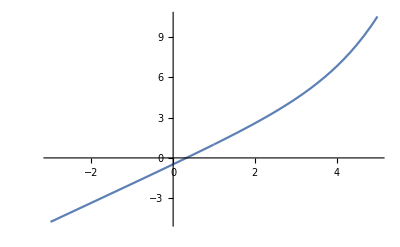

```mathematica
Plot[u1[v,Vstar,Ustar,p1],{v,-3,5}]
```

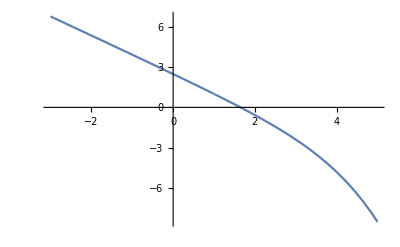

```mathematica
Plot[u2[v,Vstar,Ustar,p1],{v,-3,5}]
```

```mathematica
p2[v_]=-(2v+0.1Exp[v]);
```

```mathematica
Plot[u1[v,Vstar,Ustar,p2],{v,-3,5}]
```

-Graphics-

```mathematica
u1[v,Vstar,Ustar,p2]
```

1+(-1+v) √((-2.27183+0.1 ⅇ^v+2 v)/(-1+v))

```mathematica
Plot[u2[v,Vstar,Ustar,p2],{v,-3,5}]
```

-Graphics-

```mathematica
p3[v_]=-2v;
```

```mathematica
Plot[u1[v,Vstar,Ustar,p3],{v,-3,5}]
```

-Graphics-

```mathematica
u1[v,Vstar,Ustar,p3]
```

1+(-1+v) √((-2.27183+0.1 ⅇ^v+2 v)/(-1+v))

```mathematica
Plot[u2[v,Vstar,Ustar,p3],{v,-3,5}]
```

-Graphics-